```mathematica
s=DSolve[{q'[t]==α τ+β Sin[q[t]],q[0]==0},q,{t,0,10}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{q→Function[{t},2 ArcTan[(-β+√(-β^2+α^2 τ^2) Tan[1/2 t √(-β^2+α^2 τ^2)+ArcTan[β/(√(-β^2+α^2 τ^2))]])/(α τ)]]}}

```mathematica
s2=DSolve[{x'[t]==-2τ Sin[q[t]]/.s,x[0]==0},x,t];
```

```mathematica
F[t_]=x[t]/.s2;
f[t_]=-2 τ Sin[q[t]]/.s;
Manipulate[ Plot[{F[t]/.{α->a,β->b,τ->tau},f[t]/.{α->a,β->b,τ->tau}},{t,0,10}],{a,0.1,3},{b,0.2,3},{tau,0.1,1}]
```

```mathematica
J[t_]:=NIntegrate[-2τ Sin[q[t]]/.s,{t,0,2Pi τ/a}]
Manipulate[ Grid[{
		{Row[{"I = ",NIntegrate[-2τ Sin[q[t]]/.s,{t,0,2Pi/a}]/.{α->a,β->b,τ->tau}}]},
{Plot[f[t]/.{α->a,β->b,τ->tau},{t,0,10},ImageSize->400]}}],{a,0.1,3},{b,0.2,3},{tau,0.1,1}]
```

NIntegrate::inumr: The integrand -2 τ Sin[2 ArcTan[(-β+Power[«2»] Tan[«1»])/α]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,62.8319}}.

NIntegrate::inumr: The integrand -2 τ Sin[2 ArcTan[(-β+Power[«2»] Tan[«1»])/α]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,9.50069}}.

NIntegrate::inumr: The integrand -2 τ Sin[2 ArcTan[(-β+Power[«2»] Tan[«1»])/α]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,20.944}}.

NIntegrate::inumr: The integrand -2 τ Sin[2 ArcTan[(-β+Power[«2»] Tan[«1»])/α]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,7.75702}}.

NIntegrate::inumr: The integrand -2 τ Sin[2 ArcTan[(-β+Power[«2»] Tan[«1»])/α]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

NIntegrate::inumr: The integrand -2 τ Sin[2 ArcTan[(-β+Power[«2»] Tan[«1»])/(α τ)]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

ReplaceAll::reps: 
   {s} is neither a list of replacement rules nor a valid dispatch table, and
     so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand -2 τ Sin[q[t]] /. s
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0, 5.4875}}.

ReplaceAll::reps: 
   {s} is neither a list of replacement rules nor a valid dispatch table, and
     so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand -0.378 Sin[q[t]] /. s
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0, 5.4875}}.

ReplaceAll::reps: 
   {s} is neither a list of replacement rules nor a valid dispatch table, and
     so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

NIntegrate::inumr: 
   The integrand -0.378 Sin[q[t]] /. s
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0, 5.4875}}.

General::stop: Further output of NIntegrate::inumr
     will be suppressed during this calculation.

ReplaceAll::reps: 
   {s} is neither a list of replacement rules nor a valid dispatch table, and
     so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand -2 τ Sin[q[t]] /. s
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0, 5.4875}}.

ReplaceAll::reps: 
   {s} is neither a list of replacement rules nor a valid dispatch table, and
     so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand -0.378 Sin[q[t]] /. s
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0, 5.4875}}.

ReplaceAll::reps: 
   {s} is neither a list of replacement rules nor a valid dispatch table, and
     so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

NIntegrate::inumr: 
   The integrand -0.378 Sin[q[t]] /. s
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0, 5.4875}}.

General::stop: Further output of NIntegrate::inumr
     will be suppressed during this calculation.

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand -2 τ Sin[q[t]]/.s has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand -0.378 Sin[q[t]]/.s has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.378 Sin[q[t]]/.s has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand -2 τ Sin[q[t]]/.s has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand -0.378 Sin[q[t]]/.s has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.378 Sin[q[t]]/.s has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand -2 τ Sin[q[t]]/.s has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand -0.378 Sin[q[t]]/.s has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand -0.378 Sin[q[t]]/.s has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.4875}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
H[k_,v_]:=({{2t Cos[k a], v}, {v, -2t Cos[k a]}});
```

```mathematica
Block[{Y=H[k,v],values,vectors,U},{values,vectors}=Eigensystem[Y];
U=Transpose[Map[Normalize,vectors]]//FullSimplify;
Hdiag=Inverse[U].Y.U//FullSimplify;
U//MatrixForm]
Hdiag//MatrixForm
```

(-(-2 t Cos[a k]+√(2 t^2+v^2+2 t^2 Cos[2 a k]))/(v √(1+Abs[(-2 t Cos[a k]+√(2 t^2+v^2+2 t^2 Cos[2 a k]))/v]^2)) | (2 t Cos[a k]+√(2 t^2+v^2+2 t^2 Cos[2 a k]))/(v √(1+Abs[(2 t Cos[a k]+√(2 t^2+v^2+2 t^2 Cos[2 a k]))/v]^2))
1/(√(1+Abs[(-2 t Cos[a k]+√(2 t^2+v^2+2 t^2 Cos[2 a k]))/v]^2)) | 1/(√(1+Abs[(2 t Cos[a k]+√(2 t^2+v^2+2 t^2 Cos[2 a k]))/v]^2)))

(-√(2 t^2+v^2+2 t^2 Cos[2 a k]) | 0
0 | √(2 t^2+v^2+2 t^2 Cos[2 a k]))

```mathematica
U[[1]][[1]]
```

Part::partd: Part specification U⟦1⟧ is longer than depth of object.

U

```mathematica
Ek=Diagonal[Hdiag]
```

{-√(3+2 Cos[2 k]),√(3+2 Cos[2 k])}

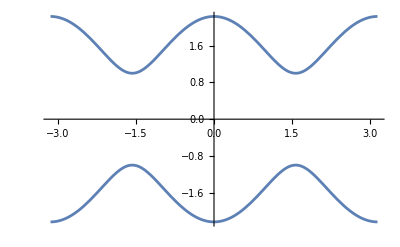

2

```mathematica
Plot[{Ek[[1]],Ek[[2]]}/.{v->1,t->1,a->1},{k,-Pi,Pi}]
Abs[Ek[[2]]-Ek[[1]]]/.{k->Pi/(2a)}
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
n:=40
q:=0.1
a:=1
t:=1
v:=1
u:=0.2
Ekk1[k2_]:=Ek[[1]]/.{k->k2}
Ekk2[k2_]:=Ek[[2]]/.{k->k2}
eqn=1/(4 u)==1/n Sum[1/(Ekk2[k]+Ekk1[k+q]-ω),{k,-Pi/(a),Pi/(a)}]
sol=Solve[eqn,ω]
```

1.25==1/40 (1/(-0.120041-ω)+1/(-0.103862-ω)+1/(-0.0410769-ω)+1/(-0.016337-ω)+1/(0.122129-ω)+1/(0.122195-ω)-1/ω)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ω→-0.1901},{ω→-0.111695},{ω→-0.0634613},{ω→-0.0269635},{ω→-0.00569677},{ω→0.0987618},{ω→0.122162}}

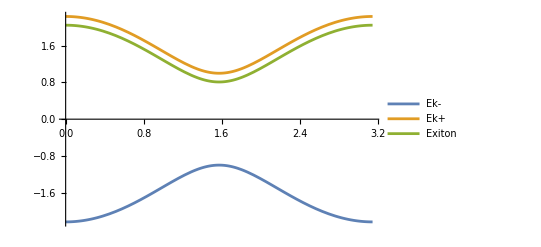

```mathematica
Plot[{Ekk1[k],Ekk2[k],Ekk2[k]+ω/.sol[[1]]},{k,0,Pi/(a)},PlotLegends->{"Ek-","Ek+","Exiton"}]
```